## Load Data

```mathematica
ClearAll["Global`*"]
mydata=Import[StringJoin[NotebookDirectory[],"data/ExampleFreezeOut.mx"]];
Keys[mydata]

dαs=mydata["Alpha"][[2;;]]-mydata["Alpha"][[1;;-2]];
αs=mydata["Alpha"];
urs=Sinh[ArcTanh[(Transpose@mydata["BackgroundFields"])[[1]]]]; (*dimensionless*)
uτs=Cosh[ArcTanh[(Transpose@mydata["BackgroundFields"])[[1]]]]; (*dimensionless*)
rs=mydata["Radius"];(*in IGeV*)
Drs=mydata["RadialDerivative"];(*in IGeV*)
τs=mydata["Time"];(*in IGeV*)
Dτs=mydata["TimeDerivative"];(*in IGeV*)
```

{BackgroundFields,Alpha,Time,Radius,NumberOfPoints,TimeDerivative,RadialDerivative,MidpointRule,rStart,tStart,CentralityClass}

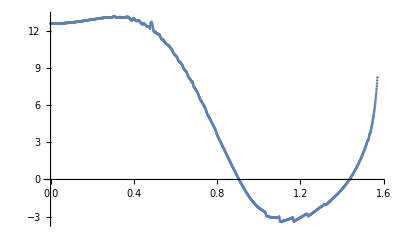

```mathematica
ListPlot[Transpose@{αs,Drs}]
```

The αs are not at all evenly spaced and their spacing varies quite discontinuously.

### Define Interpolating Functions from the Data

NOTATION: an object named "fs" (where "f" stands for any of τ,α,ur,...) refers to an array of values of the corresponding quantity evaluated on the freezeout surface, as a function of α. So Transpose{αs,fs} are the (x,y)-value pairs corresponding to the function f[α]. Here we reconstruct the corresponding functions from interpolation, assuming they are sufficiently smooth and well resolved. The necessity of interpolated functions on the FO surface becomes clear later on.

```mathematica
ur=Interpolation[Transpose@{αs,urs}];
uτ=Interpolation[Transpose@{αs,uτs}];
r=Interpolation[Transpose@{αs,rs}];
Dr=Interpolation[Transpose@{αs,Drs}];
τ=Interpolation[Transpose@{αs,τs}];
Dτ=Interpolation[Transpose@{αs,Dτs}];
```

Maybe Fitting is even better, curves will be smoother. If the data has discontinuities, so does the interpolating curve. Unlike the fitting curve.

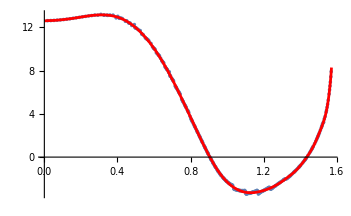

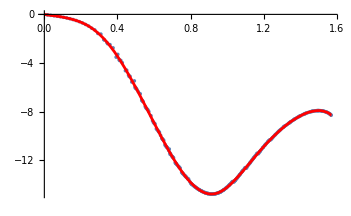

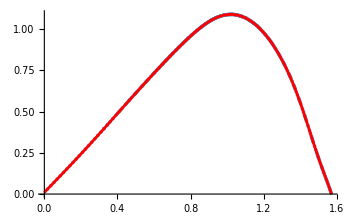

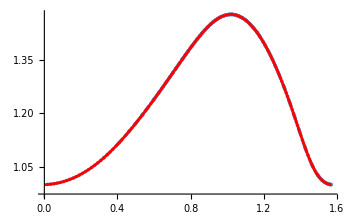

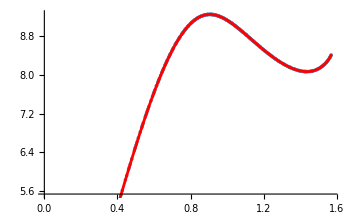

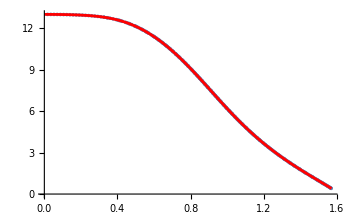

```mathematica
ndegree=55;(*14,25,43,44,55*)
monomials=Table[x^i,{i,0,ndegree}];
ur[α_]=Fit[Transpose@{αs,urs},monomials,x]/.x->α;
uτ[α_]=Fit[Transpose@{αs,uτs},monomials,x]/.x->α;
r[α_]=Fit[Transpose@{αs,rs},monomials,x]/.x->α;
Dr[α_]=Fit[Transpose@{αs,Drs},monomials,x]/.x->α;
τ[α_]=Fit[Transpose@{αs,τs},monomials,x]/.x->α;
Dτ[α_]=Fit[Transpose@{αs,Dτs},monomials,x]/.x->α;
Show[
ListPlot[Transpose@{αs,Drs}],
Plot[Dr[x],{x,0,Pi/2},PlotStyle->{Red}]
]
Show[
ListPlot[Transpose@{αs,Dτs}],
Plot[Dτ[x],{x,0,Pi/2},PlotStyle->{Red}]
]
Show[
ListPlot[Transpose@{αs,urs}],
Plot[ur[x],{x,0,Pi/2},PlotStyle->{Red}]
]
Show[
ListPlot[Transpose@{αs,uτs}],
Plot[uτ[x],{x,0,Pi/2},PlotStyle->{Red}]
]
Show[
ListPlot[Transpose@{αs,rs}],
Plot[r[x],{x,0,Pi/2},PlotStyle->{Red}]
]
Show[
ListPlot[Transpose@{αs,τs}],
Plot[τ[x],{x,0,Pi/2},PlotStyle->{Red}]
]
```

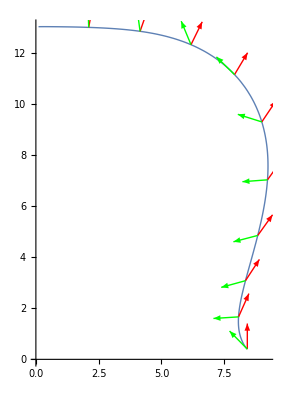

```mathematica
u[t_]=1/Sqrt[ur[t]^2+uτ[t]^2]*{ur[t],uτ[t]};
n[t_]=1/Sqrt[Dτ[t]^2+Dr[t]^2]*{Dτ[t],Dr[t]};
curve[t_]:={r[t],τ[t]};
ParametricPlot[curve[t],{t,0,Pi/2},PlotStyle->Thick,
Epilog->{{Red,Thick,Arrow[{curve@#,curve@#+u@#}]&/@Rest[Subdivide[0,Pi/2,10]]},
{Green,Thick,Arrow[{curve@#,curve@#+n@#}]&/@Rest[Subdivide[0,Pi/2,10]]}},PlotRange->Automatic]
```

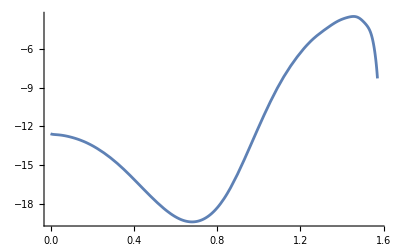

```mathematica
Plot[-Dr[t]*uτ[t]+Dτ[t]*ur[t],{t,0,Pi/2}]
```

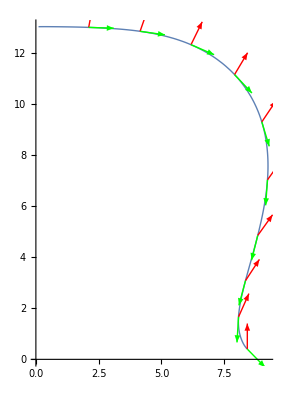

```mathematica
u[t_]=1/Sqrt[ur[t]^2+uτ[t]^2]*{ur[t],uτ[t]};
s[t_]=1/Sqrt[Dτ[t]^2+Dr[t]^2]*{Dr[t],Dτ[t]};
curve[t_]:={r[t],τ[t]};
ParametricPlot[curve[t],{t,0,Pi/2},PlotStyle->Thick,
Epilog->{{Red,Thick,Arrow[{curve@#,curve@#+u@#}]&/@Rest[Subdivide[0,Pi/2,10]]},
{Green,Thick,Arrow[{curve@#,curve@#+s@#}]&/@Rest[Subdivide[0,Pi/2,10]]}},PlotRange->Automatic]
```

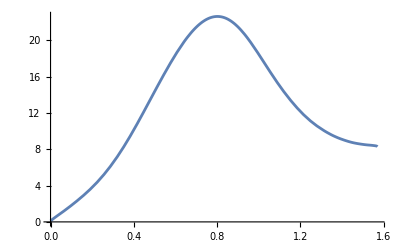

```mathematica
Plot[-Dτ[t]*uτ[t]+Dr[t]*ur[t],{t,0,Pi/2}]
```

## Compute Field on Freezeout Surface

```mathematica
GeVtoIfm=5.0677;(*5.0677;(*1GeV=5.0677(fm^-1)\[hbar]c*)*)
IfmtoGeV=1/GeVtoIfm;
fmtoIGeV=GeVtoIfm;
IGeVtofm=1/fmtoIGeV;
mσ=0.6;(*mass of the sigma field ~ 400-800 MeV*)
mπ=0.14;(*in GeV, mπ0=134.9768 MeV, mπ+-=139.57039 MeV *)
ϵ=0.001*0.160054;(*energy density at freeze out in GeV/(fm^3)*)
```

### Real fields with constant energy density

```mathematica
Subdivide[0.14,1,10]
```

{0.14,0.226,0.312,0.398,0.484,0.57,0.656,0.742,0.828,0.914,1.}

140

226

312

398

484

570

656

742

828

914

1000

InterpolatingFunction::dmval: Input value {1.58} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

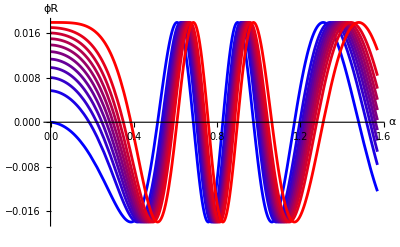

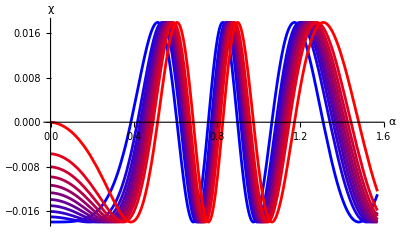

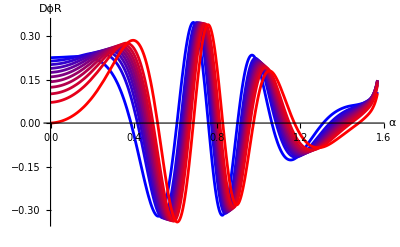

```mathematica
(*MASS IN MeV*)
Mass=140
Mass=226
Mass=312
Mass=398
Mass=484
Mass=570
Mass=656
Mass=742
Mass=828
Mass=914
Mass=1000

Mass=600

sign =-1;

description="m"<>ToString[Mass]<>"_s"<>ToString[sign]<>"_consteps";

timestamp = Block[{$DateStringFormat = {"Year", "Month", "Day", "_", "Hour", "Minute", "Second"}}, DateString[]];
plotsϕ={};
plotsχ={};
plotsDϕ={};


numi=11;
Do[
m=N@(Mass/1000);
ratio = (i-1)/(numi-1);

Epot = ratio*ϵ;
Ekin = (1 - ratio)*ϵ;
ϕRstart = Sqrt[2*Epot]/m;
χstart = sign*Sqrt[2*Ekin];

ODEs = {
      ϕR'[α] == χ[α]*(-Dτ[α]*uτ[α] + Dr[α]*ur[α]),
      χ'[α] == -m^2*ϕR[α]*(-Dτ[α]*uτ[α] + Dr[α]*ur[α])};
ICs = {ϕR[0] == ϕRstart, χ[0] == χstart};
solution = NDSolve[{ODEs, ICs}, {ϕR[α], χ[α]}, {α, 0, Pi/2}];


ϕRfunc[t_] := (ϕR[α] /. solution[[1]] /. α -> t);
χfunc[t_] := (χ[α] /. solution[[1]] /. α -> t);
DϕRfunc[t_] := (-Dr[t]*uτ[t] + Dτ[t]*ur[t])*χfunc[t];


AppendTo[plotsϕ,Plot[ϕRfunc[x], {x, 0, Pi/2}, AxesLabel -> {α, ϕR},PlotStyle->Blend[{Blue,Red},(i-1)/(numi-1)]]];
AppendTo[plotsχ,Plot[χfunc[o], {o, 0, Pi/2}, AxesLabel -> {α, χ},PlotStyle->Blend[{Blue,Red},(i-1)/(numi-1)]]];
AppendTo[plotsDϕ,Plot[DϕRfunc[o], {o, 0, Pi/2}, AxesLabel -> {α, DϕR},PlotStyle->Blend[{Blue,Red},(i-1)/(numi-1)]]];


initdata = Table[{α, Re@ϕRfunc[α], Im@ϕRfunc[α], Re@DϕRfunc[α], Im@DϕRfunc[α]}, {α, 0, Pi/2 + 0.01, .01}];
table = Prepend[
      Prepend[initdata, {"alpha", "RePhi", "ImPhi", "ReDPhi", "ImDPhi"}],
      {"# epsilon:" <> ToString[ϵ] <> "\n# mass:" <> ToString[m]<>"\n# sign:"<>ToString[sign]}];
Export[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/data/init_real_"<>description<>"_"<>timestamp<>"/init"<>ToString[i-1]<>".csv"],table,"Table","FieldSeparators"->","];
,{i,numi}]

Show[plotsϕ,PlotRange->All]
Show[plotsχ,PlotRange->All]
Show[plotsDϕ,PlotRange->All]
```

### Complex Field from Real Fields of constant energy density

```mathematica
Mass=mπ;
sign=-1;
description="piplus_composed_consteps";

timestamp = Block[{$DateStringFormat = {"Year", "Month", "Day", "_", "Hour", "Minute", "Second"}}, DateString[]];
plotsθ={};
plotsRe={};
plotsIm={};
plotsDRe={};
plotsDIm={};

ϕRs={};
DϕRs={};

numi=5;
Do[
ratio = (i-1)/(numi-1);

Epot = ratio*ϵ;
Ekin = (1 - ratio)*ϵ;
ϕRstart = Sqrt[2*Epot]/Mass;
χstart = sign*Sqrt[2*Ekin];

ODEs = {
      ϕR'[α] == χ[α]*(-Dτ[α]*uτ[α] + Dr[α]*ur[α]),
      χ'[α] == -Mass^2*ϕR[α]*(-Dτ[α]*uτ[α] + Dr[α]*ur[α])};
ICs = {ϕR[0] == ϕRstart, χ[0] == χstart};
solution = NDSolve[{ODEs, ICs}, {ϕR[α], χ[α]}, {α, 0, Pi/2}];


ϕRfunc[t_] := (ϕR[α] /. solution[[1]] /. α -> t);
χfunc[t_] := (χ[α] /. solution[[1]] /. α -> t);
DϕRfunc[t_] := (-Dr[t]*uτ[t] + Dτ[t]*ur[t])*χfunc[t];

AppendTo[ϕRs, Table[{α, Re@ϕRfunc[α]}, {α, 0, Pi/2 + 0.01, .01}]];
AppendTo[DϕRs, Table[{α, Re@DϕRfunc[α]}, {α, 0, Pi/2 + 0.01, .01}]];
,{i,numi}]

plotsRe={};
plotsIm={};
plotsDRe={};
plotsDIm={};

Do[
Do[
ϕC=1/Sqrt[2]*(Transpose@ϕRs[[i]])[[2]]-I*(Transpose@ϕRs[[j]])[[2]];
DϕC=1/Sqrt[2]*(Transpose@DϕRs[[i]])[[2]]-I*(Transpose@DϕRs[[j]])[[2]];
αs=(Transpose@ϕRs[[1]])[[1]];

(*
AppendTo[plotsRe,ListPlot[Transpose@{αs,Re@ϕC},AxesLabel->{α,Re@ϕC},PlotStyle->Blend[{Blue,Red},(i-1)/(numi-1)]]];
AppendTo[plotsIm,ListPlot[Transpose@{αs,Im@ϕC},AxesLabel->{α,Im@ϕC},PlotStyle->Blend[{Blue,Red},(i-1)/(numi-1)]]];
AppendTo[plotsDRe,ListPlot[Transpose@{αs,Re@DϕC},AxesLabel->{α,Re@DϕC},PlotStyle->Blend[{Blue,Red},(i-1)/(numi-1)]]];
AppendTo[plotsDIm,ListPlot[Transpose@{αs,Im@DϕC},AxesLabel->{α,Im@DϕC},PlotStyle->Blend[{Blue,Red},(i-1)/(numi-1)]]];
*)

initdata =Transpose@{αs, Re@ϕC, Im@ϕC, Re@DϕC, Im@DϕC};
     table = Prepend[
      Prepend[initdata, {"alpha", "RePhi", "ImPhi", "ReDPhi", "ImDPhi"}],
      {"# epsilon:" <> ToString[ϵ] <> "\n# mass:" <> ToString[Mass]<>"\n# sign:"<>ToString[sign]}];

Export[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/data/init_compl_"<>description<>"_"<>timestamp<>"/init"<>ToString[(i-1)*numi+(j-1)]<>".csv"],table,"Table","FieldSeparators"->","];

,{j,numi}]
,{i,numi}]
(*
Show[plotsRe]
Show[plotsIm]
Show[plotsDRe]
Show[plotsDIm]
*)
```

InterpolatingFunction::dmval: Input value {1.58} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

### Real Fields with Constant Amplitude and Constant Orthogonal Derivative

```mathematica
sign =1;

description="pi_constfield";

timestamp = Block[{$DateStringFormat = {"Year", "Month", "Day", "_", "Hour", "Minute", "Second"}}, DateString[]];

numi=11;
Do[
ratio = (i-1)/(numi-1);


initdata = Transpose@{{0.0,Pi/2+0.001},{N@ratio,N@ratio},{0,0},{sign*N@(1-ratio),sign*N@(1-ratio)},{0,0}};
table = Prepend[
      Prepend[initdata, {"alpha", "RePhi", "ImPhi", "ReDPhi", "ImDPhi"}],
      {"# sign:"<>ToString[sign]}];
Export[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/data/init_real_"<>description<>"_"<>timestamp<>"/init"<>ToString[i-1]<>".csv"],table,"Table","FieldSeparators"->","];
,{i,numi}]
```

### Complex Fields with Constant Amplitude and Constant Orthogonal Derivative

```mathematica
sign =-1;

description="piplus_constfield";

timestamp = Block[{$DateStringFormat = {"Year", "Month", "Day", "_", "Hour", "Minute", "Second"}}, DateString[]];

numi=5;
Do[
ratio = (i-1)/(numi-1);
Do[
relphase=Pi*(j-1)/(numi-1);
initdata = Transpose@{
{0.0,Pi/2+0.001},
{N@ratio,N@ratio},
{0,0},
{sign*Cos[relphase]*N@(1-ratio),sign*Cos[relphase]*N@(1-ratio)},
{sign*Sin[relphase]*N@(1-ratio),sign*Sin[relphase]*N@(1-ratio)}};
table = Prepend[
      Prepend[initdata, {"alpha", "RePhi", "ImPhi", "ReDPhi", "ImDPhi"}],
      {"# sign:"<>ToString[sign]}];
Export[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/data/init_comp_"<>description<>"_"<>timestamp<>"/init"<>ToString[(i-1)*numi+(j-1)]<>".csv"],table,"Table","FieldSeparators"->","];
,{j,numi}]
,{i,numi}]
```

### Real Fields with τ-dependend amplitude

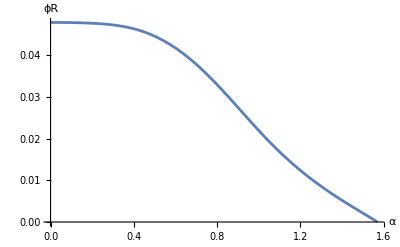

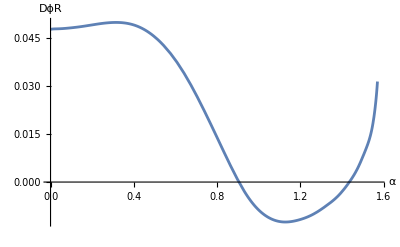

```mathematica
description="taudep";

τ0=0.4;
τf=13;
m=mπ;

ϕbar=√((2*ϵ)/m^2)/(τf-τ0);

timestamp = Block[{$DateStringFormat = {"Year", "Month", "Day", "_", "Hour", "Minute", "Second"}}, DateString[]];
plotsϕ={};
plotsDϕ={};

ϕRfunc[t_] := (τ[t]-τ0)*ϕbar;
DϕRfunc[t_] := Dr[t]*ϕbar;


AppendTo[plotsϕ,Plot[ϕRfunc[x], {x, 0, Pi/2}, AxesLabel -> {α, ϕR}]];
AppendTo[plotsDϕ,Plot[DϕRfunc[o], {o, 0, Pi/2}, AxesLabel -> {α, DϕR}]];


initdata = Table[{α, Re@ϕRfunc[α], Im@ϕRfunc[α], Re@DϕRfunc[α], Im@DϕRfunc[α]}, {α, 0, Pi/2 + 0.01, .01}];
table = Prepend[
      Prepend[initdata, {"alpha", "RePhi", "ImPhi", "ReDPhi", "ImDPhi"}],
      {"# epsilon:" <> ToString[ϵ] <> "\n# mass:" <> ToString[m]<>"\n# tau0:"<>ToString[τ0]<>"\n# tauf:"<>ToString[τf]<>"\n# ϕbar:"<>ToString[ϕbar]}];
Export[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/data/init_real_"<>description<>"_"<>timestamp<>"/init.csv"],table,"Table","FieldSeparators"->","];

Show[plotsϕ,PlotRange->All]
Show[plotsDϕ,PlotRange->All]
```

### Complex Fields with τ-dependend density

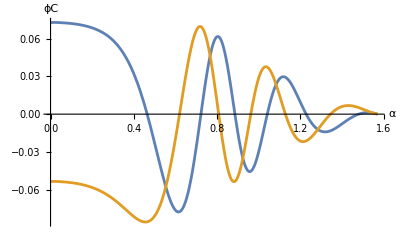

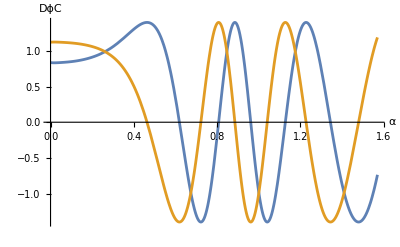

```mathematica
description="taudep";

τ0=0.4;
τf=13;
m=mπ;

nbar=√(ϵ/m^2)/(τf-τ0);

timestamp = Block[{$DateStringFormat = {"Year", "Month", "Day", "_", "Hour", "Minute", "Second"}}, DateString[]];
plotsϕ={};
plotsDϕ={};

nfunc[t_] := (τ[t]-τ0)*nbar;
θfunc[t_]:=10*m*τ[t];

ϕCfunc[t_]:=nfunc[t]*ⅇ^(ⅈ*θfunc[t]);
DϕCfunc[t_]:=(nbar+ⅈ*10*m)*ⅇ^(ⅈ*θfunc[t]);


AppendTo[plotsϕ,Plot[{Re@ϕCfunc[x], Im@ϕCfunc[x]}, {x, 0, Pi/2}, AxesLabel -> {α, ϕC}]];
AppendTo[plotsDϕ,Plot[{Re@DϕCfunc[o], Im@DϕCfunc[o]}, {o, 0, Pi/2}, AxesLabel -> {α, DϕC}]];


initdata = Table[{α, Re@ϕCfunc[α], Im@ϕCfunc[α], Re@DϕCfunc[α], Im@DϕCfunc[α]}, {α, 0, Pi/2 + 0.01, .01}];
table = Prepend[
      Prepend[initdata, {"alpha", "RePhi", "ImPhi", "ReDPhi", "ImDPhi"}],
      {"# epsilon:" <> ToString[ϵ] <> "\n# mass:" <> ToString[m]<>"\n# tau0:"<>ToString[τ0]<>"\n# tauf:"<>ToString[τf]<>"\n# nbar:"<>ToString[nbar]}];
Export[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/data/init_compl_"<>description<>"_"<>timestamp<>"/init.csv"],table,"Table","FieldSeparators"->","];

Show[plotsϕ,PlotRange->All]
Show[plotsDϕ,PlotRange->All]
```